```mathematica
u[r_]:=u0 r/r0 ⅇ^(-r/r0)
```

```mathematica
p'[r]==(ρ0+p[r] Γ/(Γ-1))u[r]^2/r
```

p'[r]==(ⅇ^(-(2 r)/r0) r u0^2 (ρ0+(Γ p[r])/(-1+Γ)))/r0^2

```mathematica
psoln=First@DSolve[{p[0]==p0,p'[r]==(ρ0+p[r] Γ/(Γ-1))u[r]^2/r},p,r];
```

```mathematica
(ρ0+p[r] Γ/(Γ-1))u[r]^2/r
```

(ⅇ^(-(2 r)/r0) r u0^2 (ρ0+(Γ p[r])/(-1+Γ)))/r0^2

```mathematica
p[r]/.psoln//FullSimplify
```

(ρ0-Γ ρ0+ⅇ^(-(ⅇ^(-(2 r)/r0) (2 r+r0-ⅇ^((2 r)/r0) r0) u0^2 Γ)/(4 r0 (-1+Γ))) (p0 Γ+(-1+Γ) ρ0))/Γ

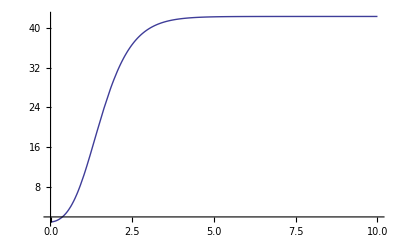

```mathematica
Plot[p[r]/.psoln/.{u0->2,Γ->1.4,r0->1,p0->1,ρ0->1},{r,0,10},PlotRange->All]
```

```mathematica
p[r]/.psoln/.{ρ0->D0,Γ->gamma}//FullSimplify//CForm
```

(D0 - D0*gamma + (D0*(-1 + gamma) + gamma*p0)/
      Power(E,(gamma*(2*r + r0 - Power(E,(2*r)/r0)*r0)*Power(u0,2))/Power(E,(2*r)/r0)/
        (4.*(-1 + gamma)*r0)))/gamma